# One-atom lasers: A semi-classical treatment

```mathematica
Needs["PlotLegends`"]
```

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Clear["Global`*"]
```

```mathematica
Eqs3={ g s12-κ a==0,-Γ/2 s12+g a s2-g s1 a-γ12/2 s12==0, -Γ/2 s13+g a s23-1/2 (γ13+γ23) s13== 0,-g a s13-1/2 (γ12+γ13+γ23) s23== 0, -Γ s1+g a s12+g s12 a+γ12 s2+γ13-γ13 s1-γ13 s2== 0,-g a s12-g s12 a+γ23-γ23 s1-γ23 s2-γ12 s2== 0};
```

```mathematica
Solgen3=Solve[Eqs3,{a,s12,s13,s23,s1,s2}]//FullSimplify
```

{{a→0,s12→0,s13→0,s23→0,s1→(γ12 (γ13+γ23))/(Γ (γ12+γ23)+γ12 (γ13+γ23)),s2→(Γ γ23)/(Γ (γ12+γ23)+γ12 (γ13+γ23))},{a→-(√(-2 g^2 (-Γ γ23+γ12 (γ13+γ23))-(Γ+γ12) (Γ (γ12+γ23)+γ12 (γ13+γ23)) κ))/(2 √(g^2 (Γ+2 (γ13+γ23)) κ)),s12→-(κ √(-2 g^2 (-Γ γ23+γ12 (γ13+γ23))-(Γ+γ12) (Γ (γ12+γ23)+γ12 (γ13+γ23)) κ))/(2 g √(g^2 (Γ+2 (γ13+γ23)) κ)),s13→0,s23→0,s1→((γ13+γ23) (2 g^2-(Γ+γ12) κ))/(2 g^2 (Γ+2 (γ13+γ23))),s2→(2 g^2 (γ13+γ23)+(Γ+γ12) (Γ+γ13+γ23) κ)/(2 g^2 (Γ+2 (γ13+γ23)))},{a→(√(-2 g^2 (-Γ γ23+γ12 (γ13+γ23))-(Γ+γ12) (Γ (γ12+γ23)+γ12 (γ13+γ23)) κ))/(2 √(g^2 (Γ+2 (γ13+γ23)) κ)),s12→(κ √(-2 g^2 (-Γ γ23+γ12 (γ13+γ23))-(Γ+γ12) (Γ (γ12+γ23)+γ12 (γ13+γ23)) κ))/(2 g √(g^2 (Γ+2 (γ13+γ23)) κ)),s13→0,s23→0,s1→((γ13+γ23) (2 g^2-(Γ+γ12) κ))/(2 g^2 (Γ+2 (γ13+γ23))),s2→(2 g^2 (γ13+γ23)+(Γ+γ12) (Γ+γ13+γ23) κ)/(2 g^2 (Γ+2 (γ13+γ23)))}}

```mathematica
n3=a a/.Solgen3
```

{0,(-2 g^2 (-Γ γ23+γ12 (γ13+γ23))-(Γ+γ12) (Γ (γ12+γ23)+γ12 (γ13+γ23)) κ)/(4 g^2 (Γ+2 (γ13+γ23)) κ),(-2 g^2 (-Γ γ23+γ12 (γ13+γ23))-(Γ+γ12) (Γ (γ12+γ23)+γ12 (γ13+γ23)) κ)/(4 g^2 (Γ+2 (γ13+γ23)) κ)}

```mathematica
nsol3=n3[[2]]
```

(-2 g^2 (-Γ γ23+γ12 (γ13+γ23))-(Γ+γ12) (Γ (γ12+γ23)+γ12 (γ13+γ23)) κ)/(4 g^2 (Γ+2 (γ13+γ23)) κ)

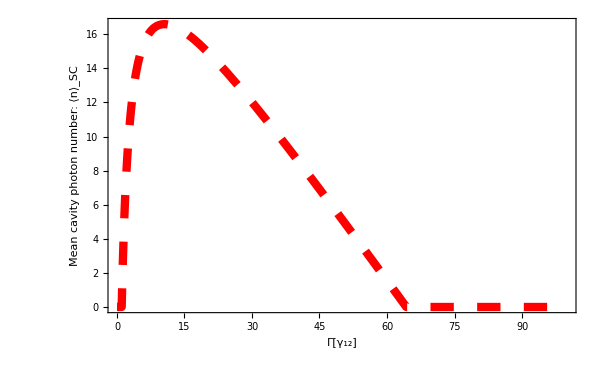

```mathematica
p1=Plot[Max[0,nsol3]/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0},{Γ,0,100},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Red,Thickness[0.01]]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","Mean cavity photon number: ⟨n⟩_SC"},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

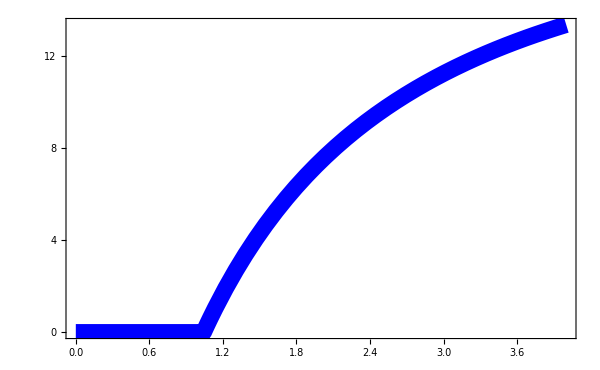

```mathematica
p2=Plot[Max[0,nsol3]/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0},{Γ,0,4},PlotStyle->{{Blue,Thickness[0.02]},{Thickness[0.012],Blue}},Frame->True,FrameTicks->{{Range[0,15,4],None},{Automatic,Automatic}},FrameLabel->{"",""},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25,Black]]
```

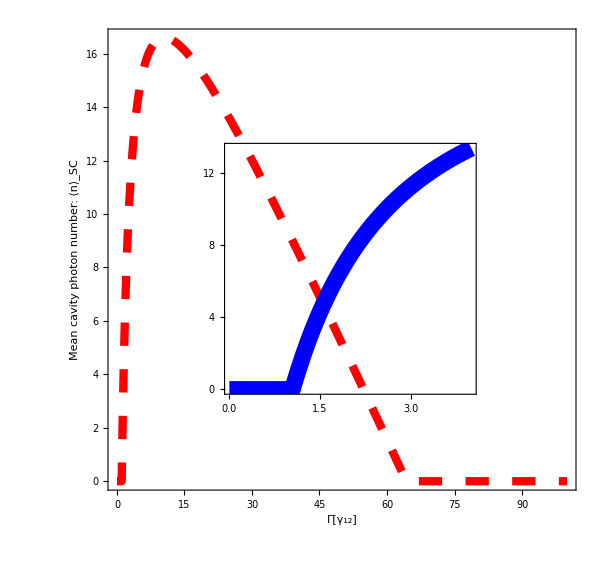

```mathematica
meanphoton=Show[Graphics[{Rectangle[{-2,1},{13,10},p1],Rectangle[{2.8,3.5},{10.2,8.0},p2]}],ImageSize->{600,580}]
```

```mathematica
Export["semi classical mean photon number.jpg",meanphoton, ImageResolution->300]
```

semi classical mean photon number.jpg

```mathematica
"semi classical mean photon number.jpg"
```

semi classical mean photon number.jpg

```mathematica
Δ123=(s2-s1)/.Solgen3
```

{(Γ γ23)/(Γ (γ12+γ23)+γ12 (γ13+γ23))-(γ12 (γ13+γ23))/(Γ (γ12+γ23)+γ12 (γ13+γ23)),-((γ13+γ23) (2 g^2-(Γ+γ12) κ))/(2 g^2 (Γ+2 (γ13+γ23)))+(2 g^2 (γ13+γ23)+(Γ+γ12) (Γ+γ13+γ23) κ)/(2 g^2 (Γ+2 (γ13+γ23))),-((γ13+γ23) (2 g^2-(Γ+γ12) κ))/(2 g^2 (Γ+2 (γ13+γ23)))+(2 g^2 (γ13+γ23)+(Γ+γ12) (Γ+γ13+γ23) κ)/(2 g^2 (Γ+2 (γ13+γ23)))}

```mathematica
Δ123one=Δ123[[1]]
```

(Γ γ23)/(Γ (γ12+γ23)+γ12 (γ13+γ23))-(γ12 (γ13+γ23))/(Γ (γ12+γ23)+γ12 (γ13+γ23))

```mathematica
Δ123two=Δ123[[2]]
```

-((γ13+γ23) (2 g^2-(Γ+γ12) κ))/(2 g^2 (Γ+2 (γ13+γ23)))+(2 g^2 (γ13+γ23)+(Γ+γ12) (Γ+γ13+γ23) κ)/(2 g^2 (Γ+2 (γ13+γ23)))

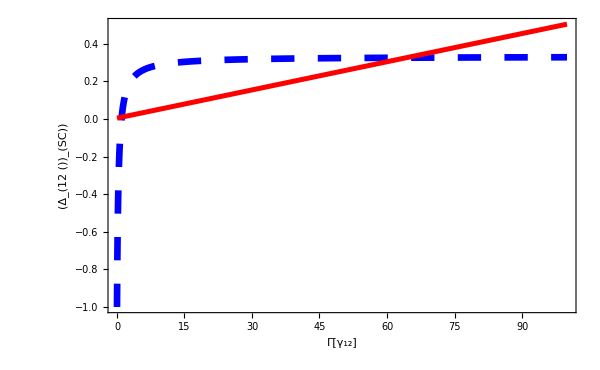

```mathematica
Plot[{Δ123one/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0},Δ123two/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0}},{Γ,0,100},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Blue,Thickness[0.008]]},{Red,Thickness[0.006]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","(Δ_(12 ())_(SC))"},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

From the above plot we can see that the threshold occurs at almost Γ=65 γ_12 therefore combining figures accordingly

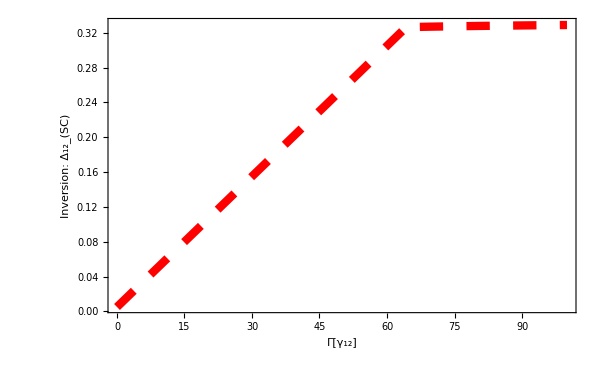

```mathematica
p3=Plot[Piecewise[{{Δ123two/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0},Γ<65},{Δ123one/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0},Γ>65}}],{Γ,0,100},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Red,Thickness[0.01]]},{Red,Thickness[0.006]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","Inversion: Δ_12_(SC)"},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

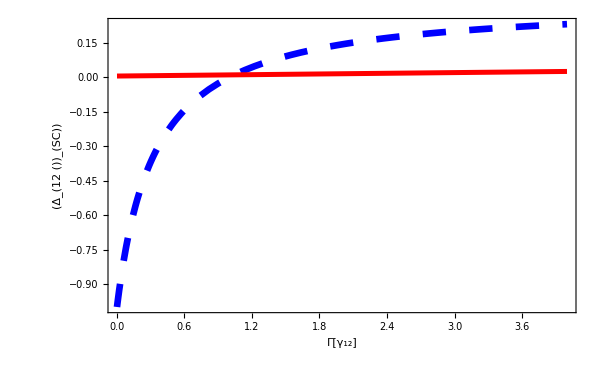

```mathematica
Plot[{Δ123one/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0},Δ123two/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0}},{Γ,0,4},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Blue,Thickness[0.008]]},{Red,Thickness[0.006]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","(Δ_(12 ())_(SC))"},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

From the above plot we can see that the threshold occurs at almost Γ=γ_12 therefore combining figures accordingly

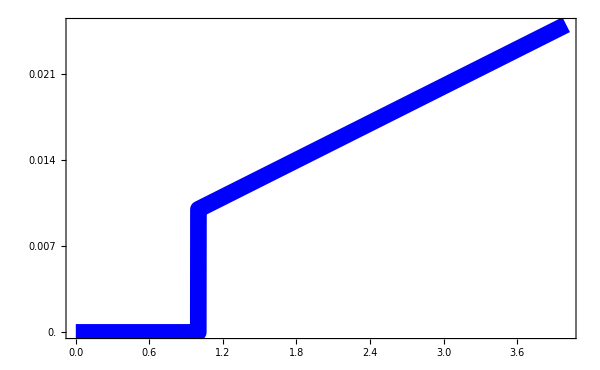

```mathematica
p4=Plot[Piecewise[{{0,Γ<1},{Δ123two/.{g-> 1, κ-> 0.01,γ12-> 1,γ23-> 0.5, γ13-> 0},Γ>1}}],{Γ,0,4},PlotStyle->{{Blue,Thickness[0.02]},{Thickness[0.012],Blue}},Frame->True,FrameTicks->{{Range[0,0.025,0.007],None}, {Automatic,Automatic}},FrameLabel->{"",""},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25,Black]]
```

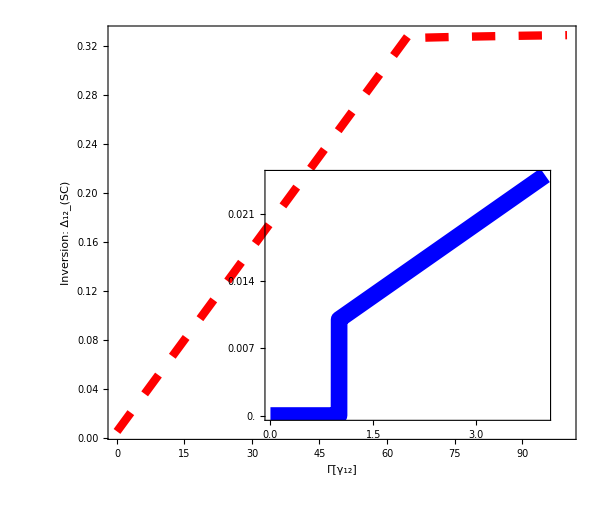

```mathematica
popinv=Show[Graphics[{Rectangle[{-2,1},{13,10},p3],Rectangle[{3.7,2.3},{12.1,7.3},p4]}],ImageSize->{600,520}]
```

```mathematica
Export["semi classical population inversion.jpg",popinv, ImageResolution->300]
```

semi classical population inversion.jpg

G3mean=(4 g^2)/(γ12+Γ+2 κ (n-0.5-√(n(n+1))));
G3mean2 = (4 g^2)/(γ12+Γ);
B=γ13+γ23+Γ;
n = γ23Γ/(2 κ B)(1-((γ23Γ+γ12B)(γ13+γ23+κ/(2 g^2)(γ12+Γ)B))/(γ23(2(γ13+γ23)+Γ)Γ));

Rst3 = (G3mean2*n *(s2 - s1)) /. Solgen3;

Rst3one = Rst3[[1]]

G3mean2 n ((Γ γ23)/(Γ (γ12+γ23)+γ12 (γ13+γ23))-(γ12 (γ13+γ23))/(Γ (γ12+γ23)+γ12 (γ13+γ23)))

Rst3two = Rst3[[2]];

Rst3three = Rst3[[3]];

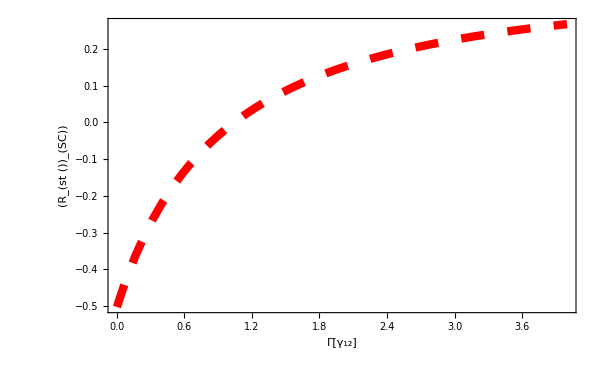

```mathematica
G3mean2=4 g^2/(γ12+Γ);

B=γ13+γ23+Γ;

n=(γ23 Γ)/(2 κ B)*(1-((γ23 Γ+γ12 B)*(γ13+γ23+(κ/(2 g^2)) (γ12+Γ) B))/(γ23 (2 (γ13+γ23)+Γ) Γ));

Rst3=FullSimplify[Evaluate[(G3mean2*n*(s2-s1))/. Solgen3]];

Rst3one=FullSimplify[Evaluate[Rst3[[1]]]];
Rst3two=FullSimplify[Evaluate[Rst3[[2]]]];
Rst3three=FullSimplify[Evaluate[Rst3[[3]]]];

expr=Evaluate[FullSimplify[Rst3three/. {g->1,κ->0.01,γ12->1,γ23->0.5,γ13->0}]];

Plot[expr,{Γ,0,4},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Red,Thickness[0.01]]},{Red,Thickness[0.006]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","(R_(st ())_(SC))"},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

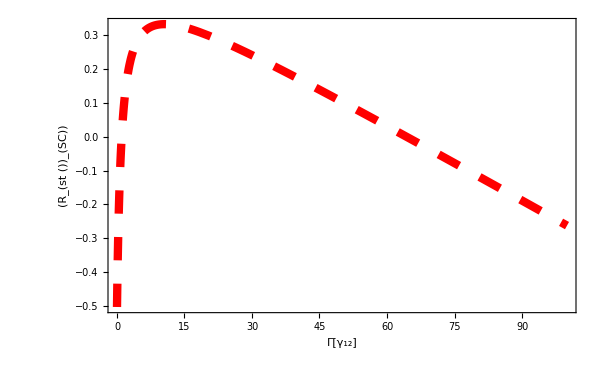

```mathematica
Plot[expr,{Γ,0,100},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Red,Thickness[0.01]]},{Red,Thickness[0.006]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","(R_(st ())_(SC))"},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

```mathematica
Rst31=FullSimplify[Evaluate[(G3mean2*n*Δ123one)]];
```

```mathematica
Rst31one = FullSimplify[Evaluate[Rst31[[1]]]];
```

```mathematica
Rst31two = FullSimplify[Evaluate[Rst31[[2]]]];
```

```mathematica
Rst32=FullSimplify[Evaluate[(G3mean2*n*Δ123two)]];
```

```mathematica
Rst32one = FullSimplify[Evaluate[Rst32[[1]]]];
```

```mathematica
Rst32two = FullSimplify[Evaluate[Rst32[[2]]]];
```

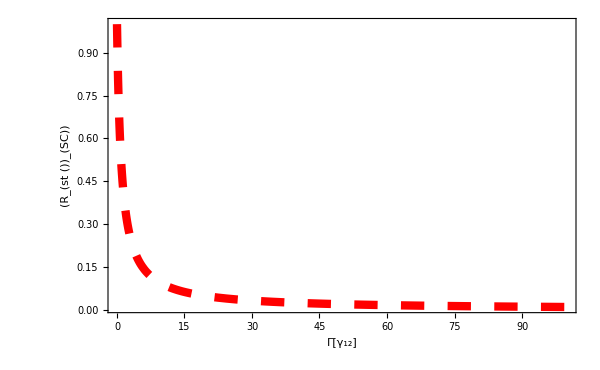

```mathematica
expr1=Evaluate[FullSimplify[Rst31two/. {g->1,κ->0.01,γ12->1,γ23->0.5,γ13->0}]];

pRsp=Plot[expr1,{Γ,0,100},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Red,Thickness[0.01]]},{Red,Thickness[0.006]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","(R_(st ())_(SC))"},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

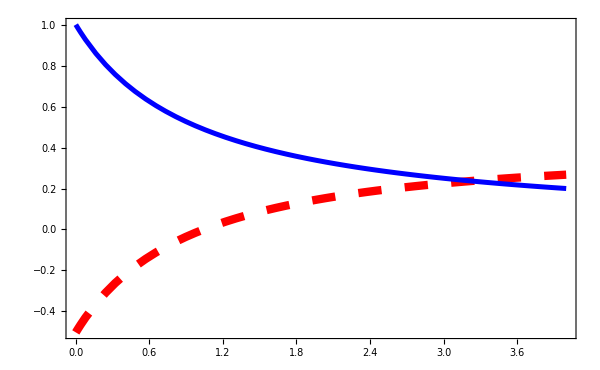

```mathematica
pRst1=Plot[{expr,expr1},{Γ,0,4},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Red,Thickness[0.01]]},{Blue,Thickness[0.006]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"",""},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

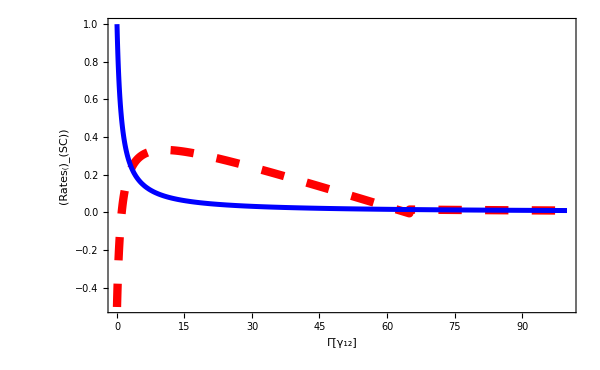

```mathematica
pRst2=ShowLegend[Plot[{Piecewise[{{Rst3three/. {g->1,κ->0.01,γ12->1,γ23->0.5,γ13->0},Γ<65},{Rst31two/. {g->1,κ->0.01,γ12->1,γ23->0.5,γ13->0},Γ>65}}],expr1},{Γ,0,100},PlotStyle->{{Directive[CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.01]]},{Blue,Thickness[0.006]},{Thickness[0.012],Blue}},Frame->True,FrameLabel->{"Γ[γ_12]","(Rates_()_(SC))"},FrameStyle->Directive[Black,AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25,Black]],{{{Graphics[{Directive[ CapForm["Round"],Dashing[{0.014 11.5,0.014 11.5}],Red,Thickness[0.1]],Line[{{0,0.5},{4,0.5}}]}],Style["Stimulated",Bold,12]},
{Graphics[{Blue,Thickness[0.07],CapForm["Round"],Line[{{0,0.5},{4,0.5}}]}],Style["Spontaneous",Bold,12]}},LegendPosition->{-0.6,0.32},LegendBackground->White,LegendBorder->Black,LegendShadow->None,LegendSize->{0.52,0.15},LegendTextSpace->1.5}]
```

```mathematica
rates=Show[Graphics[{Rectangle[{-2,1},{13,10},pRst2],Rectangle[{4.1,4.8},{12.5,9.5},pRst1]}],ImageSize->{600,520}]
```

-Graphics-

```mathematica
Export["semi classical emission rates.jpg",rates, ImageResolution->300]
```

semi classical emission rates.jpg

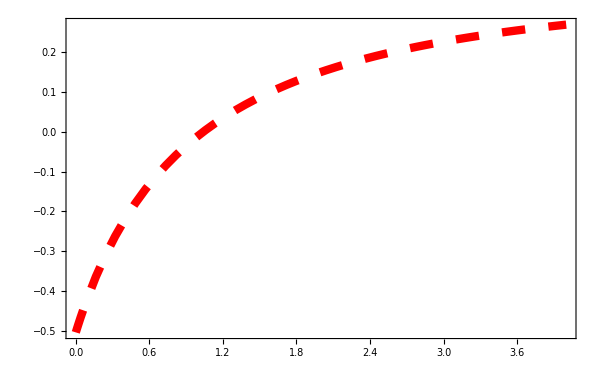

```mathematica
pRst3=Plot[expr,{Γ,0,4},PlotStyle->{{Directive[ CapForm["Round"],Dashing[{0.014 2,0.014 2}], Red,Thickness[0.01]]}},Frame->True,FrameLabel->{"",""},FrameStyle->Directive[Black, AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25, Black]]
```

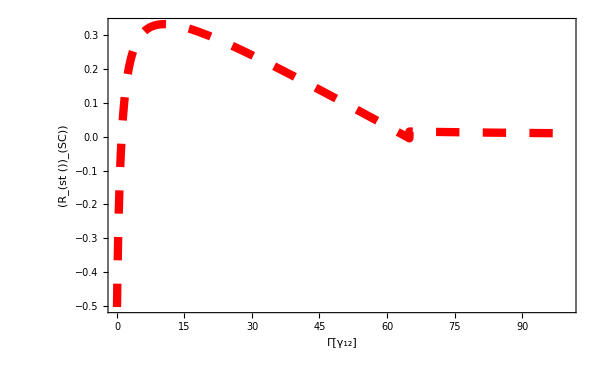

```mathematica
pRst4=Plot[{Piecewise[{{Rst3three/. {g->1,κ->0.01,γ12->1,γ23->0.5,γ13->0},Γ<65},{Rst31two/. {g->1,κ->0.01,γ12->1,γ23->0.5,γ13->0},Γ>65}}]},{Γ,0,100},PlotStyle->{{Directive[CapForm["Round"],Dashing[{0.014 2,0.014 2}],Red,Thickness[0.01]]}},Frame->True,FrameLabel->{"Γ[\!\(\*SubscriptBox[\(γ\), \ \(12\)]\)]","\!\(\*SubscriptBox[SubscriptBox[\(R\), \(st (\)], \ \(\(SC\)\()\)\)]\)"},FrameStyle->Directive[Black,AbsoluteThickness[1.25]],BaseStyle->{FontWeight->"Bold",FontSize->20},ImageSize->{600,500},PlotRange->All,PlotLabel->Style["",FontSize->25,Black]]
```

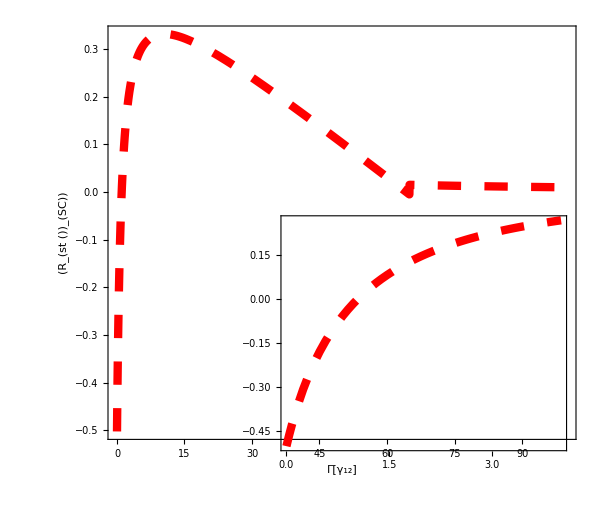

```mathematica
Show[Graphics[{Rectangle[{-2,1},{13,10},pRst4],Rectangle[{4.1,1.8},{12.5,6.5},pRst3]}],ImageSize->{600,520}]
```